## Config

```mathematica
(* Provide the location of the randgeom executable *)
(* On windows change randgeom to randgeom.exe *)
programlocation = "/home/mgv29/Desktop/randgeom"
```

/home/mgv29/Desktop/randgeom

```mathematica
(* Test the program. If it return False, check the programlocation provided. If it still does not work, first test randgeom from the console. *)
FileExistsQ[programlocation]&&ListQ[RunThrough["'"<>programlocation<>"'",""]]
```

True

## Useful functions

```mathematica
(* the following just runs randgeom with the specified parameters and parses the output as Mathematica code *)
generateMaps[type_,size_,number_]:=RunThrough["'"<>programlocation<>"' -t"<>type<>" -s"<>ToString[size]<>" -n"<>ToString[number], ""];
generateMap[type_,size_]:=First@generateMaps[type,size,1];
```

```mathematica
(* given a permutation p of {1,2,...,n}, cycles[p] gives the partition of {1,2,...,n} into cycles *)
cycles[p_]:=PermutationCycles[p,Identity];
(* given a list plist of permutations, orbits[plist] gives the partition of {1,2,...,n} into orbits under the permutations *)
orbits[plist_]:=GroupOrbits@PermutationGroup[PermutationCycles/@plist]
```

```mathematica
(* edges, vertices and faces correspond to cycles of halfedge-permutations *)
edgecycles[map_]:=cycles[map[[All,3]]];
facecycles[map_]:=cycles[map[[All,1]]];
vertexcycles[map_]:=cycles[map[[map[[All,3]],1]]];
(* We may assign id's to the vertices of map according to their position in vertexcycles[map] *)
halfedgeToVertexId[map_]:=Dispatch[Join@@MapIndexed[#1->#2[[1]]&,vertexcycles[map],{2}]];
halfedgeToFaceId[map_]:=Dispatch[Join@@MapIndexed[#1->#2[[1]]&,facecycles[map],{2}]];
```

```mathematica
(* functions to construct a Mathematica Graph object *)
uniqueEdges[map_]:=Union[Sort/@(edgecycles[map]/.halfedgeToVertexId[map])];
uniqueDualEdges[map_]:=Union[Sort/@(edgecycles[map]/.halfedgeToFaceId[map])];
mapGraph[map_]:=With[{edges=uniqueEdges[map]},Graph[Union@@edges,#[[1]]<->#[[2]]&/@edges,GraphLayout->None]];
mapDualGraph[map_]:=With[{edges=uniqueDualEdges[map]},Graph[Union@@edges,#[[1]]<->#[[2]]&/@edges,GraphLayout->None]];
```

## Plotting

```mathematica
(* the following is a bit of a hack to extract coordinates from GraphPlot3D's embedding of a graph *)
get3DGraphEmbedding[edg_,method_]:=(VertexCoordinateRules /. Cases[GraphPlot3D[#[[1]]->#[[2]]&/@edg,Method->method], _Rule, Infinity])[[Ordering@DeleteDuplicates[Join@@(List@@@edg)]]];
```

```mathematica
(* one can play with the options here to adapt the embedding *)
coordinates[map_]:=get3DGraphEmbedding[uniqueEdges[map],{"SpringElectricalEmbedding","InferentialDistance"->Automatic,"RepulsiveForcePower"->-2.4}];
```

```mathematica
(* assign colors to faces according to closeness centrality *)
colorFunction[x_]:=ColorData["Rainbow"][Round[Max[Min[0.55-0.15x,1],0],1/40]];
centralityColors[map_]:=colorFunction/@Standardize@ClosenessCentrality[mapDualGraph[map]];
```

```mathematica
plotMap3D[map_,coor_]:=Graphics3D[{EdgeForm[None],{FaceForm[#[[1]]],Polygon[coor[[#[[2,;;3]]]]],If[Length[#[[2]]]==4,Polygon[coor[[#[[2,{1,3,4}]]]]],{}]}&/@Transpose[{centralityColors[map],facecycles[map]/.halfedgeToVertexId[map]}]},Boxed->False]
```

```mathematica
map=generateMap["C",500];
plotMap3D[map,coordinates[map]]
```

Part::partd: Part specification VertexCoordinateRules⟦{1,2,3,10,4,11,12,20,23,28,«492»}⟧ is longer than depth of object.

Part::partw: Part {1,2,3} of VertexCoordinateRules⟦{1,2,3,10,4,11,12,20,23,28,«492»}⟧ does not exist.

Part::partw: Part {1,3,2} of VertexCoordinateRules⟦{1,2,3,10,4,11,12,20,23,28,«492»}⟧ does not exist.

Part::partw: Part {2,3,4} of VertexCoordinateRules⟦{1,2,3,10,4,11,12,20,23,28,«492»}⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics3D-

```mathematica
(* Task: plot geometries of various sizes and models. What are the qualitative differences between the models? *)
```

```mathematica
(* Task: produce some nice pictures. To save a nice picture, one may use something like Export["picture.png",ImageCrop@Rasterize[plot,ImageSize->800,Background->None]] *)
```

## Geodesic two-point function

```mathematica
(* Mathematica has built in support for graph distances: this returns a list of distances from all vertices to a randomly chosen vertex *)
distanceListFromRandomPoint[graph_]:=GraphDistance[graph,RandomChoice@VertexList[graph]];
```

```mathematica
(* produce a histogram with the fraction of points at distance 0,1,2,3,... *)
distanceProfile[map_,max_]:=BinCounts[#,{0,max}]/Length[#]&@distanceListFromRandomPoint@mapGraph[map];
dualDistanceProfile[map_,max_]:=BinCounts[#,{0,max}]/Length[#]&@distanceListFromRandomPoint@mapDualGraph[map];
```

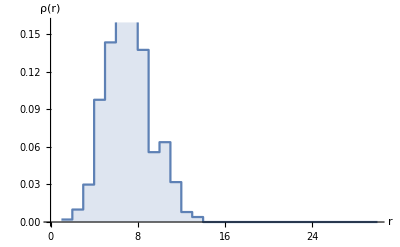

```mathematica
(* An example of a distance profile (from a random vertex) for a single random geometry *)
ListPlot[distanceProfile[generateMap["C",500],30],Joined->True,Filling->Axis,InterpolationOrder->0,AxesLabel->{"r","ρ(r)"}]
```

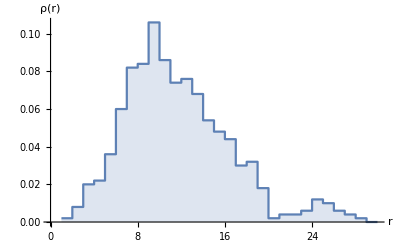

```mathematica
(* the same but for dual graph distance *)
ListPlot[dualDistanceProfile[generateMap["C",500],30],Joined->True,Filling->Axis,InterpolationOrder->0,AxesLabel->{"r","ρ(r)"}]
```

```mathematica
(* Task: Proceed to gather data for the average distance profile for different system sizes and models, and attempt finite-size scaling to extract the Hausdorff dimension *)
```

## Spectral dimension

The spectral dimension d_s of a map is related to the probability p(t) that a simple random walk on the map (or its dual) returns to its starting point after t steps: p(t) ~ t^(-d_s/2) for 1<< t << n (where n is the system size). There are various ways to measure this return probability: one can simulate a random walker and just record its returns; study a heat diffusion process; or use linear algebra as follows. The return probability ⟨p(t)⟩ averaged over all starting points of the map is related to the normalized adjacency matrix A via  ⟨p(t)⟩=Tr(A^t)/n = ∑λ_i^t/n, where λ_i are the eigenvalues of A.

```mathematica
dualAdjacencyMatrix[map_]:=Module[{dualedges,matrixentries,facedegrees},
dualedges=edgecycles[map]/.halfedgeToFaceId[map];
facedegrees=Length/@facecycles[map];
matrixentries =Tally@Join[dualedges,Reverse/@dualedges];
SparseArray[#[[1]]->#[[2]]/facedegrees[[#[[1,1]]]]&/@matrixentries]
]
```

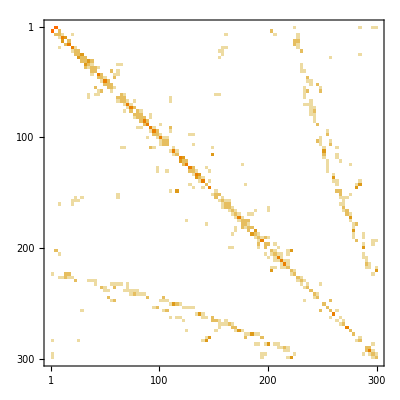

```mathematica
(* plot the adjacency matrix (for fun) *) 
MatrixPlot[dualAdjacencyMatrix[generateMap["D",300]]]
```

```mathematica
dualAdjacencySpectrum[map_]:=Sort@Eigenvalues@Normal@N@dualAdjacencyMatrix[map]
```

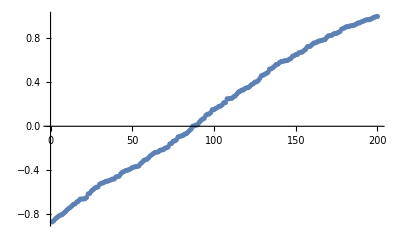

```mathematica
(* a plot of the spectrum of a random geometry *)
ListPlot[dualAdjacencySpectrum[generateMap["A",200]]]
```

```mathematica
(* The return probability of a random walker after k steps averaged over all starting points. *)
(* Notice one can may take range to be e.g. 2^Range[14] to get the return probability for {t=2,t=4,...,t=2^14} without problem. *)
returnProbability[map_,range_]:=With[{spec=dualAdjacencySpectrum[map]},Table[{t,Mean[spec^t]},{t,range}]]
```

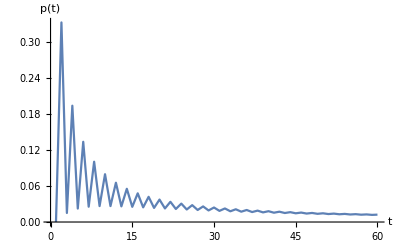

```mathematica
(* A plot of the return probability for a single random geometry *)
(* Notice the alternating pattern. Do you understand why it occurs? *)
ListPlot[returnProbability[generateMap["D",500],Range[60]],Joined->True,AxesLabel->{"t","p(t)"},PlotRange->All]
```

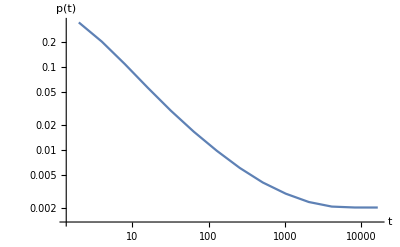

```mathematica
(* A logarithmic plot of the return probability for a single random geometry at large time, showing the finite size effects *)
(* The return probability approaches a constant at late times. What value does it take? *)
ListLogLogPlot[returnProbability[generateMap["A",500],2^Range[14]],Joined->True,AxesLabel->{"t","p(t)"}]
```

```mathematica
(* Task: Gather data for various system sizes and models and try to extract the spectral dimension by fitting the slope (in the logarithmic plot) *)
```

## Susceptibility exponent / counting exponent

Another important exponent is the susceptibility exponent γ (also known as the counting exponent) which governs the growth of the (unlabeled) partition function with increasing system size:  Z(n)~n^(γ-3)ⅇ^(-c n) (assuming we have no marking/root). One way to determine this exponent is to look for minimal necks in the map, i.e. closed paths of minimal length on the map (which for our purposes is typically length 2). For each minimal neck one may determine the distribution of the number m of faces/edges/vertices it encloses. This distribution should for large n,m be proportional to (m(n-m))^(γ-2), and fitting the data provides an estimate for γ. Be aware that for this measurement to work one needs an abundance of minimal necks, which is not necessarily the case for all models.

```mathematica
(* Below is a crude way to identify minimal necks. Do you know of a better way? *)
```

```mathematica
(* find pairs of vertices with more than one connecting edge *)
vertexPairsWithDoubleEdges[map_]:=Select[Normal@GroupBy[edgecycles[map]//Transpose[{#,#/.halfedgeToVertexId[map]}]&,Sort@Last@#&],Length[#[[2]]]>1&][[All,1]];
```

```mathematica
(* a brute force way to determine the (smallest of the two) enclosed volumes: remove the pair of vertices from the graph, and determine the sizes of the remaining connected components *)
componentSize[graph_,vertexpair_]:=Min[#,VertexCount[graph]-#]&@Length@RandomChoice@WeaklyConnectedComponents@VertexDelete[graph,vertexpair]
```

```mathematica
(* an example of the number of vertices in all the regions enclosed by minimal necks in a single random geometry *)
map=generateMap["C",200];
graph=mapGraph[map];
componentSize[mapGraph[map],#]&/@vertexPairsWithDoubleEdges[map]
```

{7,10,4,4,3,10,1,1,1,1,1,1,5,1,11,3,1,1,1,1,1,1,6,1,1,52,1,1,1,2,39,17,14,1,3,1,1,7,19,1,1,5,7,3,8,1,1,2,4,8,1,1,1,1,1,1,1,2,1,2,1,1,2,59,1,1,1,1,24,4,3,1,1,9,1,2,1,4,11,23,1,1,1,1,8,2,6}

```mathematica
(* Task: Produce histograms for the volume enclosed by minimal necks in random geometries of various sizes and models; make a logarithmic plot of the histogram (normalized by 1/V where V is the number of vertices of the geometry) against n(1-n/V) and extract γ from the slope of the curve. *)
```

## Python execution

```mathematica
session = StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
ExternalEvaluate[session, "import sys; sys.path.append(\"../2d_QG\")"]
```

```mathematica
ExternalEvaluate[session, File["../2d_QG/main.py"]]
```

n must be even

[[24, 5, 27], [16, 17, 1], [12, 26, 25], [11, 15, 9], [6, 14, 13], [10, 3, 4], [20, 22, 18], [28, 19, 29], [0, 8, 7], [2, 21, 23]]

[[25, 6, 28], [17, 18, 2], [13, 27, 26], [12, 16, 10], [7, 15, 14], [11, 4, 5], [21, 23, 19], [29, 20, 30], [1, 9, 8], [3, 22, 24]]

2

```mathematica
adj = ExternalEvaluate[session, "adj"]
```

{{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}}

```mathematica
a= {{3,29,1},{27,23,20},{18,22,12},{24,28,9},{26,15,14},{17,16,7},{21,6,19},{8,5,10},{30,13,4},{11,2,25}}
```

{{3,29,1},{27,23,20},{18,22,12},{24,28,9},{26,15,14},{17,16,7},{21,6,19},{8,5,10},{30,13,4},{11,2,25}}

## Geodesic two-point function

```mathematica
(* Mathematica has built in support for graph distances: this returns a list of distances from all vertices to a randomly chosen vertex *)
distanceListFromRandomPoint[graph_]:=GraphDistance[graph,RandomChoice@VertexList[graph]];
```

```mathematica
(* produce a histogram with the fraction of points at distance 0,1,2,3,... *)
distanceProfile[map_,max_]:=BinCounts[#,{0,max}]/Length[#]&@distanceListFromRandomPoint@mapGraph[map];
dualDistanceProfile[map_,max_]:=BinCounts[#,{0,max}]/Length[#]&@distanceListFromRandomPoint@mapDualGraph[map];
```

```mathematica
generateMap["C",200]
```

{{3,794,2},{800,797,1},{791,1,4},{8,5,3},{4,6,6},{5,8,5},{12,9,8},{6,4,7},{7,10,10},{9,12,9},{42,789,12},{10,7,11},{18,15,14},{789,42,13},{13,16,16},{15,18,15},{26,787,18},{16,13,17},{21,788,20},{787,26,19},{785,19,22},{23,786,21},{783,22,24},{757,760,23},{32,379,26},{20,17,25},{29,380,28},{379,32,27},{377,27,30},{375,378,29},{33,368,32},{28,25,31},{365,31,34},{35,366,33},{363,34,36},{40,357,35},{95,98,38},{357,40,37},{93,96,40},{38,36,39},{79,82,42},{14,11,41},{45,80,44},{588,585,43},{77,43,46},{47,78,45},{75,46,48},{49,52,47},{56,48,50},{302,299,49},{53,76,52},{48,56,51},{73,51,54},{71,74,53},{69,72,56},{52,49,55},{62,63,58},{72,69,57},{61,64,60},{63,62,59},{66,59,62},{60,57,61},{57,60,64},{59,66,63},{67,70,66},{64,61,65},{68,65,68},{70,67,67},{58,55,70},{65,68,69},{160,54,72},{55,58,71},{76,53,74},{54,160,73},{78,47,76},{51,73,75},{80,45,78},{46,75,77},{158,41,80},{43,77,79},{86,83,82},{41,158,81},{81,84,84},{83,86,83},{90,87,86},{84,81,85},{85,88,88},{87,90,87},{91,94,90},{88,85,89},{92,89,92},{94,91,91},{108,39,94},{89,92,93},{106,37,96},{39,108,95},{102,99,98},{37,106,97},{97,100,100},{99,102,99},{103,358,102},{100,97,101},{355,101,104},{353,356,103},{223,226,106},{98,95,105},{109,112,108},{96,93,107},{110,107,110},{112,109,109},{124,221,112},{107,110,111},{115,118,114},{221,124,113},{116,113,116},{118,115,115},{119,122,118},{113,116,117},{120,117,120},{122,119,119},{219,222,122},{117,120,121},{156,217,124},{114,111,123},{130,207,126},{217,156,125},{129,132,128},{207,130,127},{142,127,130},{128,125,129},{133,136,132},{127,142,131},{134,131,134},{136,133,133},{137,140,136},{131,134,135},{138,135,138},{140,137,137},{197,200,140},{135,138,139},{146,151,142},{132,129,141},{145,148,144},{151,146,143},{154,143,146},{144,141,145},{149,152,148},{143,154,147},{150,147,150},{152,149,149},{141,144,152},{147,150,151},{183,186,154},{148,145,153},{165,168,156},{126,123,155},{159,162,158},{82,79,157},{164,157,160},{74,71,159},{163,166,162},{157,164,161},{176,161,164},{162,159,163},{174,155,166},{161,176,165},{172,181,168},{155,174,167},{179,182,170},{181,172,169},{177,180,172},{170,167,171},{175,178,174},{168,165,173},{278,173,176},{166,163,175},{230,171,178},{173,278,177},{184,169,180},{171,230,179},{167,170,182},{169,184,181},{220,153,184},{182,179,183},{194,191,186},{153,220,185},{192,189,188},{191,194,187},{187,190,190},{189,192,189},{185,188,192},{190,187,191},{198,195,194},{188,185,193},{193,196,196},{195,198,195},{210,139,198},{196,193,197},{204,205,200},{139,210,199},{203,206,202},{205,204,201},{208,201,204},{202,199,203},{199,202,206},{201,208,205},{125,128,208},{206,203,207},{211,218,210},{200,197,209},{215,209,212},{216,213,211},{212,214,214},{213,216,213},{218,211,216},{214,212,215},{123,126,218},{209,215,217},{224,121,220},{186,183,219},{111,114,222},{121,224,221},{228,105,224},{222,219,223},{231,234,226},{105,228,225},{229,232,228},{226,223,227},{256,227,230},{180,177,229},{248,225,232},{227,256,231},{238,235,234},{225,248,233},{233,236,236},{235,238,235},{239,242,238},{236,233,237},{240,237,240},{242,239,239},{246,243,242},{237,240,241},{241,244,244},{243,246,243},{315,318,246},{244,241,245},{249,312,248},{234,231,247},{309,247,250},{254,251,249},{250,252,252},{251,254,251},{279,282,254},{252,250,253},{257,276,256},{232,229,255},{273,255,258},{274,271,257},{264,261,260},{271,274,259},{259,262,262},{261,264,261},{272,269,264},{262,259,263},{267,270,266},{269,272,265},{268,265,268},{270,267,267},{263,266,270},{265,268,269},{258,260,272},{266,263,271},{276,257,274},{260,258,273},{277,280,276},{255,273,275},{292,275,278},{178,175,277},{286,253,280},{275,292,279},{283,306,282},{253,286,281},{303,281,284},{285,288,283},{290,284,286},{282,279,285},{301,304,288},{284,290,287},{299,302,290},{288,285,289},{293,296,292},{280,277,291},{294,291,294},{296,293,293},{300,297,296},{291,294,295},{295,298,298},{297,300,297},{50,289,300},{298,295,299},{386,287,302},{289,50,301},{306,283,304},{287,386,303},{307,310,306},{281,303,305},{308,305,308},{310,307,307},{312,249,310},{305,308,309},{316,313,312},{247,309,311},{311,314,314},{313,316,313},{326,245,316},{314,311,315},{319,338,318},{245,326,317},{335,317,320},{321,324,319},{322,320,322},{324,321,321},{333,336,324},{320,322,323},{330,327,326},{318,315,325},{325,328,328},{327,330,327},{331,334,330},{328,325,329},{332,329,332},{334,331,331},{352,323,334},{329,332,333},{338,319,336},{323,352,335},{346,343,338},{317,335,337},{341,344,340},{343,346,339},{342,339,342},{344,341,341},{337,340,344},{339,342,343},{350,347,346},{340,337,345},{345,348,348},{347,350,347},{351,354,350},{348,345,349},{384,349,352},{336,333,351},{360,104,354},{349,384,353},{358,103,356},{104,360,355},{36,38,358},{101,355,357},{364,361,360},{356,353,359},{359,362,362},{361,364,361},{366,35,364},{362,359,363},{368,33,366},{34,363,365},{369,376,368},{31,365,367},{373,367,370},{374,371,369},{370,372,372},{371,374,371},{376,369,374},{372,370,373},{382,30,376},{367,373,375},{380,29,378},{30,382,377},{25,28,380},{27,377,379},{387,390,382},{378,375,381},{385,388,384},{354,351,383},{482,383,386},{304,301,385},{436,381,388},{383,482,387},{430,431,390},{381,436,389},{393,412,392},{431,430,391},{409,391,394},{395,402,393},{399,394,396},{400,397,395},{396,398,398},{397,400,397},{402,395,400},{398,396,399},{406,403,402},{394,399,401},{401,404,404},{403,406,403},{407,410,406},{404,401,405},{408,405,408},{410,407,407},{412,393,410},{405,408,409},{424,421,412},{391,409,411},{415,418,414},{421,424,413},{416,413,416},{418,415,415},{419,422,418},{413,416,417},{420,417,420},{422,419,419},{411,414,422},{417,420,421},{428,425,424},{414,411,423},{423,426,426},{425,428,425},{429,432,428},{426,423,427},{434,427,430},{392,389,429},{389,392,432},{427,434,431},{439,442,434},{432,429,433},{440,437,436},{390,387,435},{435,438,438},{437,440,437},{444,433,440},{438,435,439},{443,446,442},{433,444,441},{448,441,444},{442,439,443},{447,450,446},{441,448,445},{468,445,448},{446,443,447},{451,706,450},{445,468,449},{703,449,452},{460,693,451},{455,690,454},{693,460,453},{687,453,456},{457,688,455},{685,456,458},{459,462,457},{464,458,460},{454,452,459},{515,518,462},{458,464,461},{465,488,464},{462,459,463},{485,463,466},{483,486,465},{469,476,468},{450,447,467},{473,467,470},{474,471,469},{470,472,472},{471,474,471},{476,469,474},{472,470,473},{477,480,476},{467,473,475},{478,475,478},{480,477,477},{481,484,480},{475,478,479},{586,479,482},{388,385,481},{490,466,484},{479,586,483},{488,465,486},{466,490,485},{493,496,488},{463,485,487},{494,491,490},{486,483,489},{489,492,492},{491,494,491},{580,487,494},{492,489,493},{497,516,496},{487,580,495},{513,495,498},{499,502,497},{500,498,500},{502,499,499},{510,507,502},{498,500,501},{505,508,504},{507,510,503},{506,503,506},{508,505,505},{501,504,508},{503,506,507},{511,514,510},{504,501,509},{512,509,512},{514,511,511},{516,497,514},{509,512,513},{524,461,516},{495,513,515},{522,683,518},{461,524,517},{525,528,520},{683,522,519},{523,526,522},{520,517,521},{546,521,524},{518,515,523},{530,519,526},{521,546,525},{529,532,528},{519,530,527},{544,527,530},{528,525,529},{533,680,532},{527,544,531},{677,531,534},{542,539,533},{540,537,536},{539,542,535},{535,538,538},{537,540,537},{534,536,540},{538,535,539},{675,678,542},{536,534,541},{549,552,544},{532,529,543},{550,547,546},{526,523,545},{545,548,548},{547,550,547},{566,543,550},{548,545,549},{556,553,552},{543,566,551},{551,554,554},{553,556,553},{564,665,556},{554,551,555},{559,666,558},{665,564,557},{663,557,560},{561,656,559},{653,560,562},{651,654,561},{569,572,564},{558,555,563},{567,570,566},{552,549,565},{568,565,568},{570,567,567},{578,563,570},{565,568,569},{573,576,572},{563,578,571},{574,571,574},{576,573,573},{589,592,576},{571,574,575},{587,590,578},{572,569,577},{581,584,580},{496,493,579},{582,579,582},{584,581,581},{585,588,584},{579,582,583},{44,583,586},{484,481,585},{756,577,588},{583,44,587},{692,575,590},{577,756,589},{596,605,592},{575,692,591},{603,606,594},{605,596,593},{604,601,596},{594,591,595},{599,602,598},{601,604,597},{600,597,600},{602,599,599},{595,598,602},{597,600,601},{608,593,604},{598,595,603},{591,594,606},{593,608,605},{614,649,608},{606,603,607},{611,650,610},{649,614,609},{647,609,612},{637,640,611},{615,638,614},{610,607,613},{635,613,616},{636,633,615},{626,627,618},{633,636,617},{624,621,620},{627,626,619},{619,622,622},{621,624,621},{625,628,624},{622,619,623},{630,623,626},{620,617,625},{617,620,628},{623,630,627},{631,634,630},{628,625,629},{632,629,632},{634,631,631},{616,618,634},{629,632,633},{638,615,636},{618,616,635},{652,612,638},{613,635,637},{644,641,640},{612,652,639},{639,642,642},{641,644,641},{648,645,644},{642,639,643},{643,646,646},{645,648,645},{650,611,648},{646,643,647},{607,610,650},{609,647,649},{668,562,652},{640,637,651},{656,561,654},{562,668,653},{660,657,656},{560,653,655},{655,658,658},{657,660,657},{661,664,660},{658,655,659},{662,659,662},{664,661,661},{666,559,664},{659,662,663},{555,558,666},{557,663,665},{669,672,668},{654,651,667},{670,667,670},{672,669,669},{673,676,672},{667,670,671},{674,671,674},{676,673,673},{686,541,676},{671,674,675},{680,533,678},{541,686,677},{681,684,680},{531,677,679},{682,679,682},{684,681,681},{517,520,684},{679,682,683},{688,457,686},{678,675,685},{690,455,688},{456,685,687},{691,694,690},{453,687,689},{696,689,692},{592,589,691},{452,454,694},{689,696,693},{700,701,696},{694,691,695},{699,702,698},{701,700,697},{704,697,700},{698,695,699},{695,698,702},{697,704,701},{706,451,704},{702,699,703},{746,751,706},{449,703,705},{724,749,708},{751,746,707},{714,735,710},{749,724,709},{725,728,712},{735,714,711},{718,715,714},{712,709,713},{713,716,716},{715,718,715},{719,722,718},{716,713,717},{720,717,720},{722,719,719},{723,726,722},{717,720,721},{744,721,724},{710,707,723},{738,711,726},{721,744,725},{729,732,728},{711,738,727},{730,727,730},{732,729,729},{733,736,732},{727,730,731},{734,731,734},{736,733,733},{709,712,736},{731,734,735},{742,739,738},{728,725,737},{737,740,740},{739,742,739},{747,750,742},{740,737,741},{745,748,744},{726,723,743},{754,743,746},{708,705,745},{752,741,748},{743,754,747},{707,710,750},{741,752,749},{705,708,752},{750,747,751},{755,758,754},{748,745,753},{792,753,756},{590,587,755},{790,24,758},{753,792,757},{768,765,760},{24,790,759},{763,766,762},{765,768,761},{764,761,764},{766,763,763},{759,762,766},{761,764,765},{769,784,768},{762,759,767},{781,767,770},{782,779,769},{773,776,772},{779,782,771},{774,771,774},{776,773,773},{777,780,776},{771,774,775},{778,775,778},{780,777,777},{770,772,780},{775,778,779},{784,769,782},{772,770,781},{786,23,784},{767,781,783},{788,21,786},{22,783,785},{17,20,788},{19,785,787},{11,14,790},{760,757,789},{794,3,792},{758,755,791},{798,799,794},{1,791,793},{797,800,796},{799,798,795},{2,795,798},{796,793,797},{793,796,800},{795,2,799}}

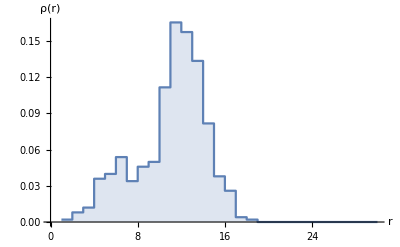

```mathematica
(* An example of a distance profile (from a random vertex) for a single random geometry *)
ListPlot[distanceProfile[generateMap["C",500],30],Joined->True,Filling->Axis,InterpolationOrder->0,AxesLabel->{"r","ρ(r)"}]
```

```mathematica
distanceProfile[adj, 10]
```

PermutationCycles::permlist: Invalid permutation list {28,2,26,10,14,5,19,30,8,24}.

Part::partw: Part {28,2,26,10,14,5,19,30,8,24} of {{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}} does not exist.

PermutationCycles::perm: {{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}}⟦{28,2,26,10,14,5,19,30,8,24},1⟧ is not a valid permutation.

Part::pkspec1: The expression {28,2,26,10,14,5,19,30,8,24}→1 cannot be used as a part specification.

PermutationCycles::perm: ({{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}}→1)⟦{28,2,26,10,14,5,19,30,8,24}→1,1→1⟧ is not a valid permutation.

ReplaceAll::reps: {Dispatch[Join[({{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}}→1)⟦{28,2,26,10,14,5,19,30,8,24}→1,1→1⟧,Identity]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

PermutationCycles::perm: Identity is not a valid permutation.

General::stop: Further output of PermutationCycles::perm will be suppressed during this calculation.

ReplaceAll::reps: {Dispatch[Join[({{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}}→1)⟦{28,2,26,10,14,5,19,30,8,24}→1,1→1⟧,Identity]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {PermutationCycles[Identity,{28,2,26,10,14,5,19,30,8,24}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Union::heads: Heads PermutationCycles and Dispatch at positions 2 and 1 are expected to be the same.

Part::partw: Part 2 of Dispatch[Join[({{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}}→1)⟦{28,2,26,10,14,5,19,30,8,24}→1,1→1⟧,Identity]] does not exist.

VertexList::graph: A graph object is expected at position 1 in VertexList[Graph[Dispatch[Join[({«10»}→1)⟦{«10»}→1,1→1⟧,Identity]]∪PermutationCycles[Identity,{28,2,26,10,14,5,19,30,8,24}],Join[({«10»}→1)⟦{«10»}→1,1→1⟧,Identity]<->Dispatch[Join[Part[«3»],Identity]]⟦2⟧/.Identity<->{28,2,26,10,14,5,19,30,8,24},GraphLayout→None]].

RandomChoice::lrwl: The items for choice VertexList[Graph[Dispatch[Join[({«10»}→1)⟦{«10»}→1,1→1⟧,Identity]]∪PermutationCycles[Identity,{28,2,26,10,14,5,19,30,8,24}],Join[({«10»}→1)⟦{«10»}→1,1→1⟧,Identity]<->Dispatch[Join[Part[«3»],Identity]]⟦2⟧/.Identity<->{28,2,26,10,14,5,19,30,8,24},GraphLayout→None]] should be a non-empty list or a rule weights -> choices.

GraphDistance::graph: A graph object is expected at position 1 in GraphDistance[Graph[Dispatch[Join[({«10»}→1)⟦{«10»}→1,1→1⟧,Identity]]∪PermutationCycles[Identity,{28,2,26,10,14,5,19,30,8,24}],Join[({«10»}→1)⟦{«10»}→1,1→1⟧,Identity]<->Dispatch[Join[Part[«3»],Identity]]⟦2⟧/.Identity<->{28,2,26,10,14,5,19,30,8,24},GraphLayout→None],RandomChoice[VertexList[Graph[Dispatch[Join[Part[«3»],Identity]]∪PermutationCycles[Identity,{28,2,26,10,14,5,19,30,8,24}],Join[Part[«3»],Identity]<->Dispatch[«1»]⟦2⟧/.Identity<->{28,2,26,10,14,5,19,30,8,24},GraphLayout→None]]]].

BinCounts::vectmat: The first argument is expected to be a vector or matrix.

1/2 BinCounts[GraphDistance[Graph[Dispatch[Join[({{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}}→1)⟦{28,2,26,10,14,5,19,30,8,24}→1,1→1⟧,Identity]]∪PermutationCycles[Identity,{28,2,26,10,14,5,19,30,8,24}],Join[({{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}}→1)⟦{28,2,26,10,14,5,19,30,8,24}→1,1→1⟧,Identity]<->Dispatch[Join[({{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}}→1)⟦{28,2,26,10,14,5,19,30,8,24}→1,1→1⟧,Identity]]⟦2⟧/.Identity<->{28,2,26,10,14,5,19,30,8,24},GraphLayout→None],RandomChoice[VertexList[Graph[Dispatch[Join[({{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}}→1)⟦{28,2,26,10,14,5,19,30,8,24}→1,1→1⟧,Identity]]∪PermutationCycles[Identity,{28,2,26,10,14,5,19,30,8,24}],Join[({{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}}→1)⟦{28,2,26,10,14,5,19,30,8,24}→1,1→1⟧,Identity]<->Dispatch[Join[({{25,6,28},{17,18,2},{13,27,26},{12,16,10},{7,15,14},{11,4,5},{21,23,19},{29,20,30},{1,9,8},{3,22,24}}→1)⟦{28,2,26,10,14,5,19,30,8,24}→1,1→1⟧,Identity]]⟦2⟧/.Identity<->{28,2,26,10,14,5,19,30,8,24},GraphLayout→None]]]],{0,10}]

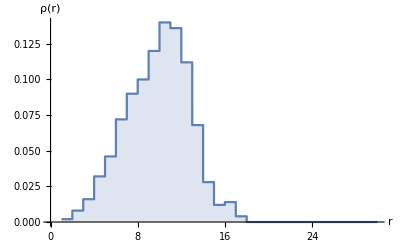

```mathematica
(* the same but for dual graph distance *)
ListPlot[dualDistanceProfile[generateMap["C",500],30],Joined->True,Filling->Axis,InterpolationOrder->0,AxesLabel->{"r","ρ(r)"}]
```

```mathematica
(* Task: Proceed to gather data for the average distance profile for different system sizes and models, and attempt finite-size scaling to extract the Hausdorff dimension *)
```